Calculate the data size of an entire image and the scanning time
TB: binary vs decimal basis, http://knowledge.seagate.com/articles/en_US/FAQ/194563en

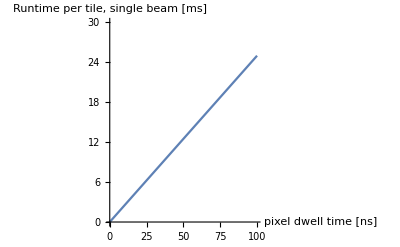

```mathematica
μm = 10^-6;
μs=10^-6;
ms=10^-3;
ns = 10^-9;
mm=10^-3;
Tera=10^12; (*Decimal base*)
kHz=10^3;
Mega=10^6;
Giga = 10^9;
byte=8;

bpp=8; (*Bits per pixel*)
Δx=0.5μm;(*Spatial sampling rate in x and y. Optical resolution is twice this*)
Δz=0.5 μm;(*Spatial sampling in z. The pptical resolution is twice this*)
Lz=0.5mm;(*Section thickness*)
FOV=0.25mm;(*Tile size*)
γ=0.8;(*Prefactor that accounts for the dead time at the turning points*)
Tline=1/(2*8 kHz);(*Scanning time per line. The resonant scanner does a round trip in 8kHz*)
Npix= FOV/Δx ;(*A tile has a total of Npix^2 pixels*)
dwellTime=γ Tline/Npix;(*Dwell time [s/pix]*)

Ttile[n_] := Npix*Tline/n(*Scanning time per tile. n is the number of beamlets. Note that the dead time at the turning points must be considered*)

Ntiles[L_]:=(L/FOV)^2(*Number of tiles in a plane*)
Npixz[L_]:=L/Δz(*Total number of pixels in the z direction*)
Npixtotal[L_]:=(L/Δx)^2 L/Δz(*Total number of pixels in the sample*)
time[L_,n_]:=Ntiles[L] Npixz[L]Ttile[n] (*Scanning time per sample (per channel). Shifting time between tiles not considered*)

Plot[Npix^2 *t ns/ms,{t,0,100},PlotRange->{0,0.03/ms},AxesLabel->{"pixel dwell time [ns]","Runtime per tile, single beam [ms]"}]
```

```mathematica
Ntiles[10mm]
```

1600.

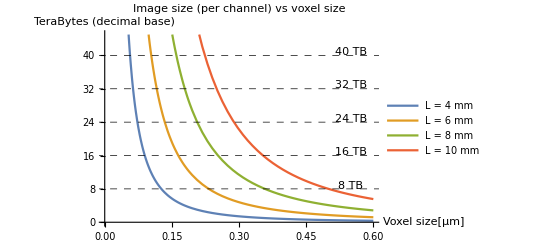

```mathematica
DataSize[L_,Δx_]:=(L/Δx)^2(L/Δz)*bpp  (*Data size in bits PER CHANNEL*)
Show[Plot[Evaluate[Table[DataSize[dummy mm,dummy2 μm],{dummy,4,10,2}]/(Tera*byte)],{dummy2,0.05,0.6},AxesOrigin->{0,0},PlotRange->{0,45},PlotLegends-> {"L = 4 mm","L = 6 mm","L = 8 mm","L = 10 mm"},AxesLabel->{"Voxel size[μm]","TeraBytes (decimal base)"},GridLines->{{},{8,16,24,32,40}},GridLinesStyle->Directive[Black, Dashed],PlotLabel->"Image size (per channel) vs voxel size"],Graphics[Table[Text[ToString[i]"TB",{0.55,i+.8}],{i,8,40,8}]]]
```

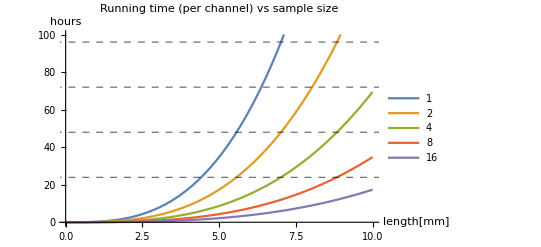

```mathematica
(*Running time PER CHANNEL*)
Plot[Evaluate[Table[time[dummy mm,2^i]/3600,{i,0,4}]],{dummy,0,10},PlotRange->{0,100},AxesLabel->{"length[mm]","hours"},PlotLegends->Table[2^i,{i,0,6}],GridLines->{{},{24,48,72,96}},GridLinesStyle->Directive[Black, Dashed],PlotLabel->"Running time (per channel) vs sample size"]
```

```mathematica
L=10mm; (*Sample size*)
Npixtotal[L]
1/Ttile[1](*frames (tiles) per second*)
```

8.×10^12

32.

How much time does it take to fully transfer a 8TB (decimal base) HDD

```mathematica
HDD=8*Tera*byte; (*Max HDD capacity in bits*)
busrate=10 10^9;(*Transfer rate in bps*)
1.*HDD/busrate/3600 (*Time to transfer a 8TB HDD [in hours]*)
```

1.77778

```mathematica
(*Data-saving speed required [MB/s] for 16 beamlets. A commercial HDD writes at 150 MB/s*)
16 FOV/Δx bpp/(Tline*Mega*byte)
```

128.

```mathematica
(*Quick estimations*)
L=10mm; (*sample size*)
Δx=0.5μm;
bpp=8; (*bits per pixel*)
3(L/Δx)^3 bpp 1/(Tera*byte)(*Data size for 3 channels*)
```

24.

```mathematica
(*Runtime for 3 channel [hours]*)
3 L^3/Δx^2 Tline/(FOV*16)/3600
```

52.0833